# Noise Node discovery

## Load Nodes List

```mathematica
root = "D:/";
```

```mathematica
root="~/research/posecpp";
```

```mathematica
home = $HomeDirectory
```

/home/lichao

```mathematica
noisy= ToExpression//@StringSplit/@ReadList[root<>"/geo/converge_n.txt",Record];
```

## Find Noisy ones

```mathematica
noisy=noisy/.{false->False,true->True};
```

```mathematica
Tally[Total[#[[2;;]]]&/@noisy]
```

{{False+10 True,118},{11 False,113},{11 True,387},{2 False+9 True,5},{10 False+True,13},{8 False+3 True,1},{9 False+2 True,5},{6 False+5 True,1},{3 False+8 True,1},{7 False+4 True,1}}

```mathematica
noisylist=Select[noisy,Last[#]==True&][[;;,1]]
```

{11,16,19,21,29,30,34,35,38,41,50,51,52,55,58,61,67,68,76,81,83,86,92,93,95,102,108,109,111,115,120,133,142,144,148,150,154,156,159,166,173,177,180,181,182,184,190,193,196,197,207,210,211,213,215,216,220,227,232,233,234,236,245,250,252,255,263,269,271,278,282,283,284,299,300,301,303,305,307,309,312,314,316,322,325,326,329,332,339,343,344,347,348,351,352,358,363,368,369,370,372,379,384,385,386,387,388,389,392,393,395,402,403,404,410,412,415,416,424,428,431,432,434,435,436,440,441,443,448,449,455,456,458,461,465,469,474,475,477,478,484,487,492,493,497,500,501,502,505,507,512,513,518,519,520,521,522,523,525,526,529,532,536,538,539,542,543,545,548,549,556,560,561,563,570,573,575,576,578,579,580,582,583,587,589,594,595,596,598,603,604,605,606,607,608,610,611,615,620,623,624,625,627,632,633,634,637,639,641,642,645,647,656,658,659,660,663,664,666,671,675,678,685,688,694,696,698,700,710,712,713,714,715,718,719,720,725,727,733,736,737,742,745,753,755,757,759,764,765,766,771,772,773,775,776,790,792,797,804,805,806,811,815,817,822,826,827,830,836,838,841,844,845,847,849,852,855,857,860,861,862,870,875,884,885,886,887,889,890,891,894,895,897,899,902,903,915,918,920,922,923,927,929,936,937,943,946,949,951,952,953,955,956,957,961,962,966,969,973,981,982,985,988,990,995,998,1000,1003,1004,1005}

```mathematica
Length[noisy]
```

645

```mathematica
Length[noisylist]
```

330

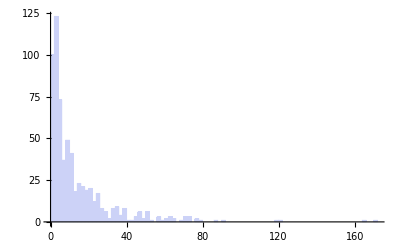

```mathematica
Histogram[#[[2]]&/@noisy,100]
```

```mathematica
noisy//TableForm;
```

## Compare with our headlist

```mathematica
corelist = ReadList[home<>"/git/posecpp/res/core_head_clusters_52.txt"]
```

{20,594,239,613,423,652,958}

```mathematica
headlist = ReadList[home<>"/git/posecpp/res/head_clusters_52.txt"]
```

{0,20,74,112,113,124,131,176,184,201,221,222,238,239,277,331,338,354,370,392,396,419,423,454,458,462,467,485,517,526,542,562,585,593,594,613,652,662,706,748,807,818,821,861,876,893,898,942,958,967,978,1004}

```mathematica
badList = {124,392,818,585,542,113}
```

{124,392,818,585,542,113}

```mathematica
Intersection[badList,noisylist]
```

{392,542}

```mathematica
Intersection[corelist,noisylist]
```

{594}

```mathematica
Intersection[headlist,noisylist]
```

{184,370,392,458,526,542,594,861,1004}

```mathematica
noisy[[;;,{1,10,11,12}]]//MatrixForm;
```